```mathematica
ClearAll["Global`*"]
```

```mathematica
lo[n_, k_ ]:= Sum[ (-1)^(j+1) lo[ Floor[n/j],k-1],{j,1,n}];lo[n_, 1] := Sum[ (-1)^(j+1) Log[j],{j,1,n}]
t[n_, a_] := Mod[n,a]-Mod[n-1,a]
lp[n_, k_,b_ ]:= Sum[ t[j,b] lp[ Floor[n/j],k-1,b],{j,1,n}];lp[n_, 1,b_] := Sum[ t[j,b] Log[j],{j,1,n}]
fa[n_,k_] := Sum[ 2^j Binomial[k,j] (-1)^j l1[n/2^j,k],{j,0,k}]+Sum[ 2^j Binomial[k-1,j-1](-1)^j Log[2] d1[n/2^j,k],{j,1,k}]

L1[n_, k_ ]:= Sum[ L1[Floor[n/j],k-1],{j,1,n}];L1[n_, 1] := Sum[ Log[j],{j,1,n}];L1[n_,0]:=1
L2[n_, k_ ]:= Sum[ L2[Floor[n/j],k-1],{j,2,n}];L2[n_, 1] := Sum[ Log[j],{j,2,n}]
D1[n_, k_] := Sum[ D1[Floor[n/j],k-1],{j,1,n}];D1[n_, 0] := 1
L2toL1[n_,z_]:=Sum[FactorialPower[z-1,a]/a! L2[n,a+1],{a,0,Log[2,n]}]
L2toL1x[n_,z_]:=Sum[Binomial[z-1,a] L2[n,a+1],{a,0,Log[2,n]}]
L1toL2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k-1,j-1] L1[n,j],{j,1,k}]

EL[n_, k_,b_ ]:= EL[n,k,b]=Sum[ EL[ n/j,k-1,b],{j,1,n}]-b Sum[ EL[ n/(j b),k-1,b],{j,1,n}];EL[n_, 1,b_] := EL[n,1,b]=Sum[ Log[j],{j,1,n}]-b Sum[ Log[j b],{j,1,n/b}]
LtoEL[n_,k_,b_] := Sum[ b^j Binomial[k,j] (-1)^j L1[n/b^j,k],{j,0,k}]+Sum[ b^j Binomial[k-1,j-1](-1)^j Log[b] D1[n/b^j,k],{j,1,k}]

EL1toL1[n_, b_] := Sum[ b^j EL[n/b^j,1,b],{j,0,Log[b,n]}] + Log[b]Sum[ b^j D1[n/b^j,1],{j,1,Log[b,n]}]

EL2[n_, k_,b_ ]:= EL2[n,k,b]=Sum[ EL2[ n/j,k-1,b],{j,2,n}]-Sum[ EL2[ n/(j b),k-1,b],{j,1,n}];EL2[n_, 1,b_] := EL2[n,1,b]=Sum[ Log[j],{j,2,n}]-Sum[ Log[j b],{j,1,n/b}]
EL2toEL1[n_,z_,b_]:=Sum[FactorialPower[z-1,a]/a! EL2[n,a+1,b],{a,0,Log[If[ b<2,b,2],n]}]
EL1toEL2[n_,k_,b_]:=Sum[(-1)^(k-j) Binomial[k-1,j-1] EL[n,j,b],{j,1,k}]
```

```mathematica
N[L2toL1x[100,0]]
```

94.0453

```mathematica
N[EL2toEL1[100,0,101]]
```

94.0453

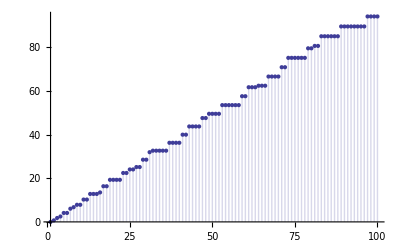

```mathematica
DiscretePlot[L2toL1[n,0],{n,1,100}]
```

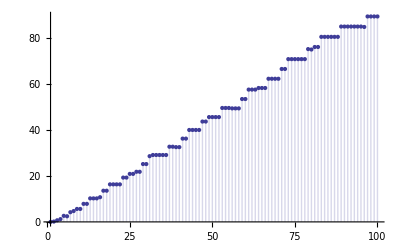

```mathematica
DiscretePlot[EL2toEL1[n,0,1.2],{n,1,100}]
```

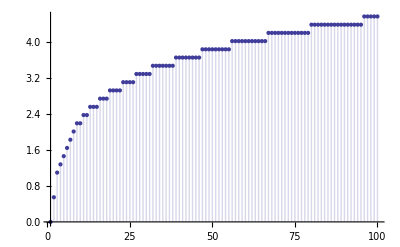

```mathematica
DiscretePlot[L2toL1[n,0]-EL2toEL1[n,0,1.2],{n,1,100}]
```

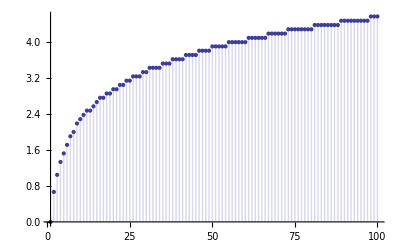

```mathematica
DiscretePlot[L2toL1[n,0]-EL2toEL1[n,0,1.1],{n,1,100}]
```

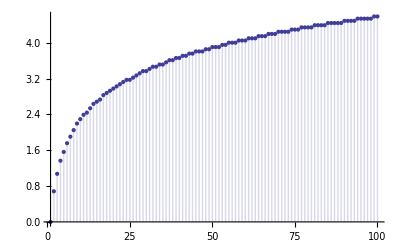

```mathematica
DiscretePlot[L2toL1[n,0]-EL2toEL1[n,0,1.05],{n,1,100}]
```

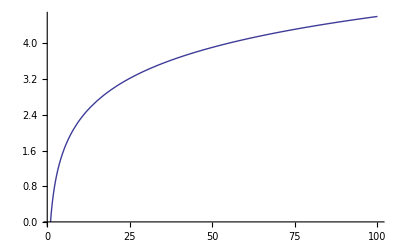

```mathematica
Plot[Log[n],{n,1,100}]
```

```mathematica
N[Log[2 Pi]]
```

1.83788

```mathematica
fdif[n_,b_] := Sum[ Log[b],{j,1,Log[b,n]}]
```

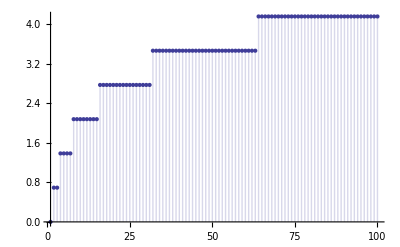

```mathematica
DiscretePlot[L2toL1[n,0]-EL2toEL1[n,0,2],{n,1,100}]
```

```mathematica
DiscretePlot[fdif[n,2],{n,1,100}]
```

-Graphics-

```mathematica
N[Table[{n,L2toL1[n,0]-EL2toEL1[n,0,2]},{n,1,100}]]//TableForm
```

1. | 0.
2. | 0.693147
3. | 0.693147
4. | 1.38629
5. | 1.38629
6. | 1.38629
7. | 1.38629
8. | 2.07944
9. | 2.07944
10. | 2.07944
11. | 2.07944
12. | 2.07944
13. | 2.07944
14. | 2.07944
15. | 2.07944
16. | 2.77259
17. | 2.77259
18. | 2.77259
19. | 2.77259
20. | 2.77259
21. | 2.77259
22. | 2.77259
23. | 2.77259
24. | 2.77259
25. | 2.77259
26. | 2.77259
27. | 2.77259
28. | 2.77259
29. | 2.77259
30. | 2.77259
31. | 2.77259
32. | 3.46574
33. | 3.46574
34. | 3.46574
35. | 3.46574
36. | 3.46574
37. | 3.46574
38. | 3.46574
39. | 3.46574
40. | 3.46574
41. | 3.46574
42. | 3.46574
43. | 3.46574
44. | 3.46574
45. | 3.46574
46. | 3.46574
47. | 3.46574
48. | 3.46574
49. | 3.46574
50. | 3.46574
51. | 3.46574
52. | 3.46574
53. | 3.46574
54. | 3.46574
55. | 3.46574
56. | 3.46574
57. | 3.46574
58. | 3.46574
59. | 3.46574
60. | 3.46574
61. | 3.46574
62. | 3.46574
63. | 3.46574
64. | 4.15888
65. | 4.15888
66. | 4.15888
67. | 4.15888
68. | 4.15888
69. | 4.15888
70. | 4.15888
71. | 4.15888
72. | 4.15888
73. | 4.15888
74. | 4.15888
75. | 4.15888
76. | 4.15888
77. | 4.15888
78. | 4.15888
79. | 4.15888
80. | 4.15888
81. | 4.15888
82. | 4.15888
83. | 4.15888
84. | 4.15888
85. | 4.15888
86. | 4.15888
87. | 4.15888
88. | 4.15888
89. | 4.15888
90. | 4.15888
91. | 4.15888
92. | 4.15888
93. | 4.15888
94. | 4.15888
95. | 4.15888
96. | 4.15888
97. | 4.15888
98. | 4.15888
99. | 4.15888
100. | 4.15888

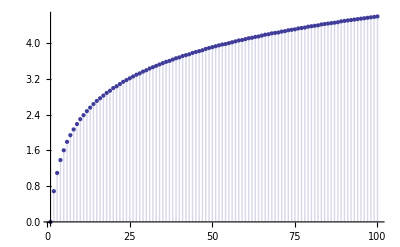

```mathematica
DiscretePlot[fdif[n,1.01],{n,1,100}]
```

```mathematica
Limit[Sum[ Log[b],{j,1,Log[b,n]}],b->1]
```

Log[n]